# Comparing σHe-4 to Schwaller

## Micah Buuck

7/24/13

## Define constants

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
ℏc=197.32697178(*Mega ElectronVolt*Femto Meter*);
m=938.272046(*Mega ElectronVolt*);
mn=1.00137842*m(*Mega ElectronVolt*);
r=.535^(-1/2)(*Femto Meter*);
```

## Import data

```mathematica
(*Bdata=Import["/Users/Micah/Documents/JerryDuty/eikexp/B.csv"];
npdata=Import["/Users/Micah/Documents/JerryDuty/eikexp/npsig.csv"];
pndata=Import["/Users/Micah/Documents/JerryDuty/eikexp/pnsig.csv"];
σpndata=Union[npdata,pndata];
αpndata=Import["/Users/Micah/Documents/JerryDuty/eikexp/pnepsilon.csv"];
σppdata=Import["/Users/Micah/Documents/JerryDuty/eikexp/ppsig.csv"];
αppdata=Import["/Users/Micah/Documents/JerryDuty/eikexp/ppepsilon.csv"];*)
```

```mathematica
Bdata=Import["/phys/users/mbuuck/JerryDuty/eikexp/B.csv"];
npdata=Import["/phys/users/mbuuck/JerryDuty/eikexp/npsig.csv"];
pndata=Import["/phys/users/mbuuck/JerryDuty/eikexp/pnsig.csv"];
σpndata=Union[npdata,pndata];
αpndata=Import["/phys/users/mbuuck/JerryDuty/eikexp/pnepsilon.csv"];
σppdata=Import["/phys/users/mbuuck/JerryDuty/eikexp/ppsig.csv"];
αppdata=Import["/phys/users/mbuuck/JerryDuty/eikexp/ppepsilon.csv"];
```

```mathematica
(*Bdata (*Taken from Schwaller ref 63; slope parameter for scattering amplitude of pp scattering*)
σpndata(*Taken from PDG website; total σ for pn and np collisions*)
αpndata(*From PDG; Re[f(0)]/Im[f(0)] for pn collisions*)
σppdata(*From PDG; total σ for pp collisions*)
αppdata(*From PDG; Re[f(0)]/Im[f(0)] for pp collisions*)*)
```

```mathematica
(*σHe4data={{{224,106.3},ErrorBar[1.3]},{{273,105.7},ErrorBar[1.3]},{{345,106.8},ErrorBar[1.1]},{{413,110.8},ErrorBar[1.2]},{{430,112.8},ErrorBar[1.0]},{{491,117.6},ErrorBar[1.5]},{{563,123.7},ErrorBar[0.9]}};*)
```

```mathematica
σHe4data={{224,106.3},{273,105.7},{345,106.8},{413,110.8},{430,112.8},{491,117.6},{563,123.7}};
```

## Do a linear fit of the B data:

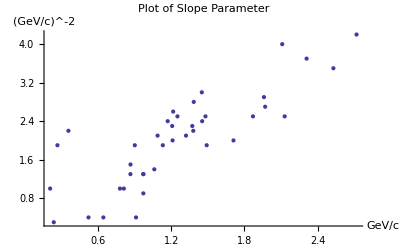

```mathematica
ListPlot[Bdata[[All,1;;2]],PlotLabel->"Plot of Slope Parameter",AxesLabel->{"GeV/c","(GeV/c)^-2"}]
```

```mathematica
Bmodel=LinearModelFit[Bdata[[All,1;;2]],x,x]
```

FittedModel[0.401428+1.29697 x]

```mathematica
Clear[B]
```

```mathematica
Bfunc[x_]=Bmodel["BestFit"];
```

Get slope parameter in units and form matching Schwaller paper:

```mathematica
gamma[En_(*MeV*)]=Sqrt[Bfunc[Sqrt[(En/1000)^2+2*m/1000*En/1000]]]*(ℏc/1000)*Sqrt[2](*fm*);
```

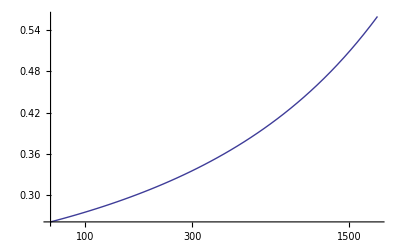

```mathematica
LogLinearPlot[gamma[En],{En,70,2000}]
```

## Fit Bezier Curve to σ and α data

```mathematica
σpnbf=BezierFunction[DeleteDuplicates[Log[σpndata],#1[[1]]==#2[[1]]&]];
```

```mathematica
Show[Graphics[{Red,Point[Log[σpndata]]},Axes->True],ParametricPlot[σpnbf[t],{t,0,1}],PlotLabel->"Log-Log Plot of total σ for pn scattering with fitted curve",AxesLabel->{Log[p]"in GeV/c  ",Log[σ]"in mb  "}]
```

-Graphics-

```mathematica
σpnbf[[3]]
```

{592}

```mathematica
σpng=Interpolation[σpnbf/@Range[0,1,.001]];
```

It takes some processing to get the fit into a useable function

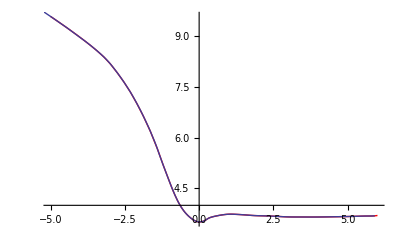

```mathematica
σpnp1=Plot[σpng[x],{x,-5,6},PlotStyle->Red];
σpnp2=ParametricPlot[σpnbf[t],{t,0,1}];
Show[σpnp1,σpnp2]
```

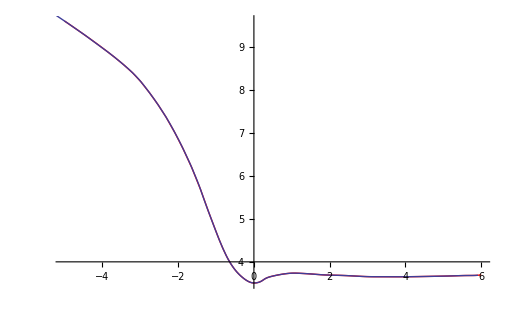

-Graphics-

```mathematica
σpn[En_(*MeV*)]=Exp[σpng[Log[Sqrt[(En/1000)^2+2*m/1000*En/1000]]]]/10;
```

The line above unlogs the Bezier fit and converts it into the right units (fm^2).

```mathematica
σpn[2000](*in fm^2*)
```

4.19813

The plot below shows that it fits the raw unloged data well.

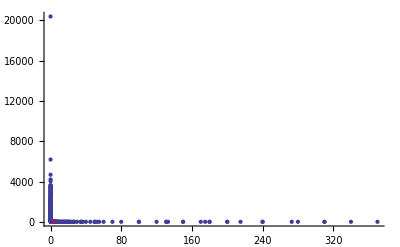

```mathematica
Show[ListPlot[σpndata],Plot[Exp[σpng[Log[x]]],{x,.00385,7},PlotStyle->Red]]
```

Now we repeat the same process for α, and then for both σand α for pp scattering.

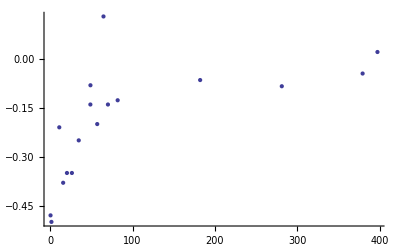

```mathematica
ListPlot[αpndata]
```

```mathematica
αpnbf=BezierFunction[DeleteDuplicates[αpndata,#1[[1]]==#2[[1]]&]];
```

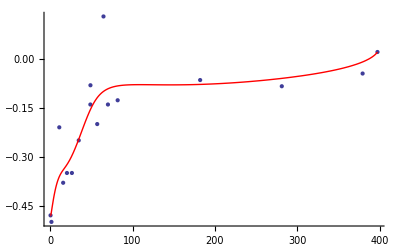

```mathematica
Show[ListPlot[αpndata],ParametricPlot[αpnbf[t],{t,0,1},PlotStyle->Red]]
```

```mathematica
αpng=Interpolation[αpnbf/@Range[0,1,.001]];
```

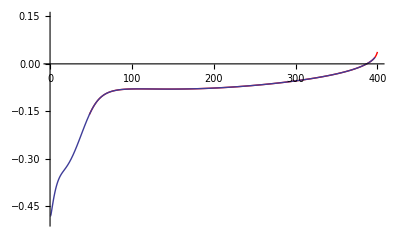

```mathematica
αpnp1=Quiet[Plot[αpng[x],{x,0,400},PlotStyle->Red]];
αpnp2=ParametricPlot[αpnbf[t],{t,0,1}];
Show[αpnp1,αpnp2,PlotRange->{-.5,.15}]
```

```mathematica
αpn[En_(*MeV*)]:=αpng[Sqrt[(En/1000)^2+2*m/1000*En/1000]]
```

```mathematica
σppbf=BezierFunction[DeleteDuplicates[Log[σppdata],#1[[1]]==#2[[1]]&]];
```

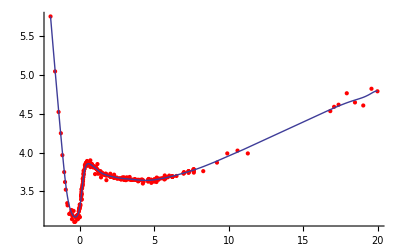

```mathematica
Show[ListPlot[Log[σppdata],PlotStyle->Red],ParametricPlot[σppbf[t],{t,0,1}]]
```

```mathematica
σppg=Interpolation[σppbf/@Range[0,1,.001]]
```

InterpolatingFunction[{{-1.96611,19.9893}},<>]

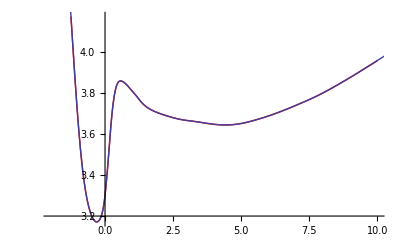

```mathematica
σppp1=Quiet[Plot[σppg[x],{x,-2,10},PlotStyle->Red]];
σppp2=ParametricPlot[σppbf[t],{t,0,1}];
Show[σppp1,σppp2]
```

```mathematica
σpp[En_(*MeV*)]=Exp[σppg[Log[Sqrt[(En/1000)^2+2*m/1000*En/1000]]]]/10;
```

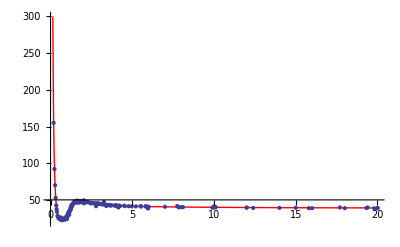

```mathematica
Show[Plot[Exp[σppg[Log[x]]],{x,.14,20},PlotStyle->Red,PlotRange->{{0,20},{20,300}}],ListPlot[σppdata]]
```

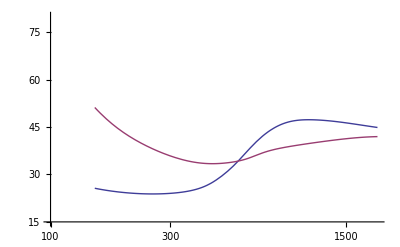

```mathematica
Quiet[LogLinearPlot[{10*σpp[En],10*σpn[En]},{En,150,2000},PlotRange->{{100,2000},{15,80}}]]
```

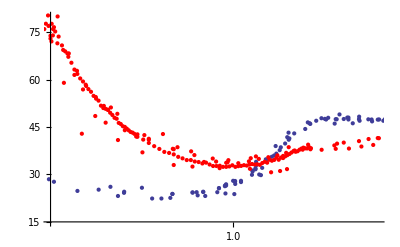

```mathematica
Show[ListLogLinearPlot[σppdata,PlotRange->{{Sqrt[2*m/1000*100/1000],Sqrt[2*m/1000*2000/1000]},{15,80}}],ListLogLinearPlot[σpndata,PlotStyle->Red]]
```

Take average of σpn and σpp to get nucleon-nucleon scattering. (This is what Schwaller does.)

```mathematica
σ[En_(*MeV*)]=(σpp[En]+σpn[En])/2;
```

```mathematica
σ[2000]
```

4.34266

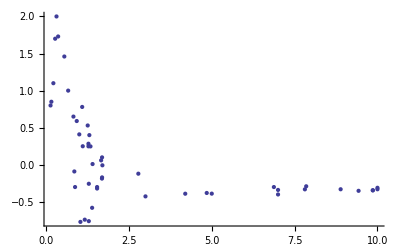

```mathematica
ListPlot[αppdata]
```

```mathematica
αppbf=BezierFunction[DeleteDuplicates[αppdata,#1[[1]]==#2[[1]]&]];
```

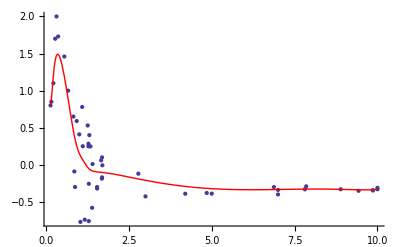

```mathematica
Show[ListPlot[αppdata],ParametricPlot[αppbf[t],{t,0,1},PlotStyle->Red]]
```

```mathematica
αppg=Interpolation[αppbf/@Range[0,1,.001]];
```

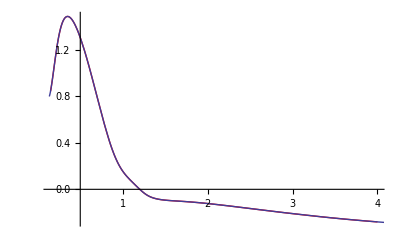

```mathematica
αppp1=Plot[αppg[x],{x,.15,4},PlotStyle->Red];
αppp2=ParametricPlot[αppbf[t],{t,0,1}];
Show[αppp1,αppp2]
```

```mathematica
αpp[En_(*MeV*)]:=αppg[Sqrt[(En/1000)^2+2*m/1000*En/1000]]
```

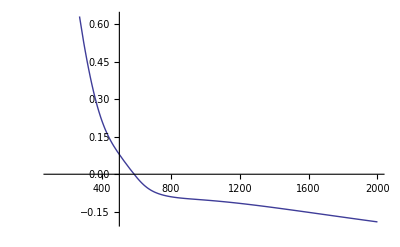

```mathematica
Plot[αpp[En],{En,100,2000}]
```

Take average of αpn and αpp to get α for nucleon-nucleon scattering.

```mathematica
(*α[En_(*MeV*)]=If[En<500,Log[500/En],Log[500/En]/2];*)
α[En_(*MeV*)]=(αpn[En]+αpp[En])/2;
```

This average might not be so good, because the energy range in question only contains about two data points for αpn. There are many more data points for αpp in the energy region of interest, so it may just be better to take αpp as the overall α instead of an average (or perhaps use some sort of weighting process).

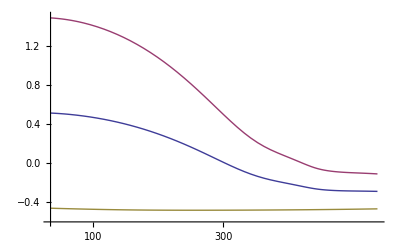

```mathematica
Quiet[LogLinearPlot[{α[En],αpp[En],αpn[En]},{En,70,1100},PlotRange->{-.6,1.5}]]
```

```mathematica
σHe4[En_(*MeV*)]:=20*Pi*r^2*(1+2*r^(-2)*gamma[En]^2)*Sum[Binomial[4,j]*(-1)^(j+1)/j*(σ[En]/(2*Pi*r^2*(1+2*r^-2*gamma[En]^2)))^j*Re[(1-I*α[En])^j],{j,1,4}](*This is in mb*)
```

```mathematica
σHe4[500]
```

108.627

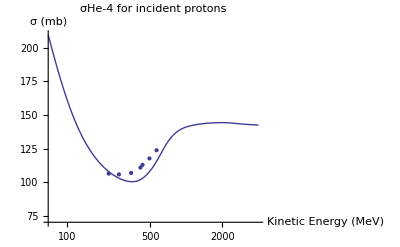

```mathematica
σHe4LLP=Quiet[LogLinearPlot[σHe4[En],{En,70,4000},PlotRange->{{70,4000},{70,210}},PlotLabel->"σHe-4 for incident protons",AxesLabel->{"Kinetic Energy (MeV)","σ (mb)"}]];
σHe4LP=ListLogLinearPlot[σHe4data];
Show[σHe4LLP,σHe4LP]
```

This plot seems to roughly follow what Schwaller has in his paper. There seems to be some disagreement at low energies. At ~150 MeV, Schwaller’s σ ≃ 160 mb, but I have σ ≃ 120 mb. This actually seems to fit the data better than Schwaller’s analysis, which is strange, since I followed it as best I could. My best guess as to what may be causing this discrepancy is that I believe he was using values for his slope parameter that were quite different from mine. He comments that above about 500 MeV, a value of gamma^2 = 0.3 fm^2 seems to fit the data well. That does not agree with what I found:

```mathematica
gamma[500]^2
```

0.141362

It is also possible that the more recent and probably accurate data I am using from the PDG is better than what he had, and that that helps with accuracy.

Here I can test the effect using αpp instead of α has on the calculation:

```mathematica
σHe41[En_(*MeV*)]:=20*Pi*r^2*(1+2*r^(-2)*gamma[En]^2)*Sum[Binomial[4,j]*(-1)^(j+1)/j*(σ[En]/(2*Pi*r^2*(1+2*r^-2*gamma[En]^2)))^j*Re[(1-I*αpp[En])^j],{j,1,4}](*This is in mb*)
```

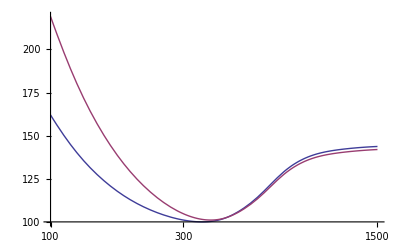

```mathematica
Quiet[LogLinearPlot[{σHe4[En],σHe41[En]},{En,100,1500}]]
```

It appears to have quite a large effect. This is alarming, since the data for αpn was so sparse.

With just some very basic eyeballing, it looks like the fits that Schwaller made for α are approximately the curve below. Check out Fig 7 (solid line) and compare:

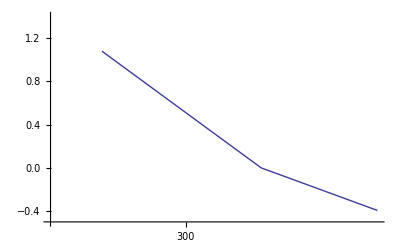

```mathematica
LogLinearPlot[If[x<500,Log[500/x],Log[500/x]/2],{x,170,1100},PlotRange->{{120,1100},{-.5,1.4}}]
```

```mathematica
rC12=.263^(-1/2);
```

```mathematica
σC12[En_]:=20*Pi*rC12^2*(1+2*rC12^(-2)*gamma[En]^2)*Sum[Binomial[12,j]*(-1)^(j+1)/j*(σ[En]/(2*Pi*rC12^2*(1+2*rC12^-2*gamma[En]^2)))^j*Re[(1-I*α[En])^j],{j,1,12}](*This is in mb*)
```

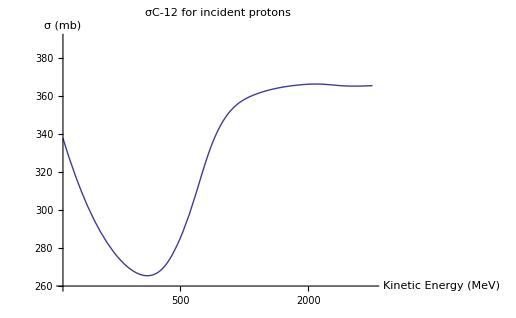

```mathematica
Quiet[LogLinearPlot[σC12[En],{En,140,4000},PlotRange->{{140,4000},{260,390}},PlotLabel->"σC-12 for incident protons",AxesLabel->{"Kinetic Energy (MeV)","σ (mb)"}]]
```

```mathematica
rO16=.233^(-1/2);
```

```mathematica
σO16[En_]:=20*Pi*rO16^2*(1+2*rO16^(-2)*gamma[En]^2)*Sum[Binomial[16,j]*(-1)^(j+1)/j*(σ[En]/(2*Pi*rO16^2*(1+2*rO16^-2*gamma[En]^2)))^j*Re[(1-I*α[En])^j],{j,1,16}](*This is in mb*)
```

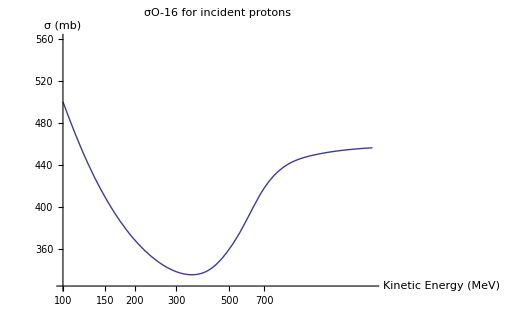

```mathematica
Quiet[LogLinearPlot[σO16[En],{En,100,2000},PlotRange->{{100,2000},{325,560}},PlotLabel->"σO-16 for incident protons",AxesLabel->{"Kinetic Energy (MeV)","σ (mb)"}]]
```

```mathematica
rH2=.2^(-1/2);
```

```mathematica
σH2[En_]:=20*Pi*rH2^2*(1+2*rH2^(-2)*gamma[En]^2)*Sum[Binomial[2,j]*(-1)^(j+1)/j*(σ[En]/(2*Pi*rH2^2*(1+2*rH2^-2*gamma[En]^2)))^j*Re[(1-I*α[En])^j],{j,1,2}]
```

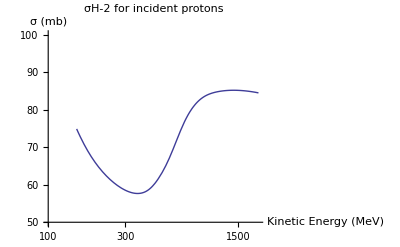

```mathematica
Quiet[LogLinearPlot[σH2[En],{En,150,2000},PlotRange->{{100,2000},{50,100}},PlotLabel->"σH-2 for incident protons",AxesLabel->{"Kinetic Energy (MeV)","σ (mb)"}]]
```

## Add in first order correction

Going to switch over to Wallace's notation now:

My apologies: this section is a bit of a mess right now.

```mathematica
m=0.938272046;(*GeV/c^2*)
mn=1.00137842*m(*GeV/c^2*);
M=2*m+2*mn;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
gamma[En_(*GeV*)]:=Sqrt[Bfunc[Sqrt[En^2+2*m*En]]]*ℏc*Sqrt[2](*fm*)
β[En_(*GeV*)]:=1/2*gamma[En]^2/ℏc^2(*(c/GeV)^2*)
B:=1/4*r^2/ℏc^2(*(c/GeV)^2*)
αpn[En_(*GeV*)]:=αpng[Sqrt[En^2+2*m*En]]
αpp[En_(*GeV*)]:=αppg[Sqrt[En^2+2*m*En]]
α[En_(*GeV*)]:=(αpp[En]+αpn[En])/2
ρ[En_(*GeV*)]:=α[En]
σpn[En_(*GeV*)]:=Exp[σpng[Log[Sqrt[En^2+2*m*En]]]]/10
σpp[En_(*GeV*)]:=Exp[σppg[Log[Sqrt[En^2+2*m*En]]]]/10
σ[En_(*GeV*)]:=(σpp[En]+σpn[En])/2
σ1[En_(*GeV*)]:=σ[En]*(1-I*ρ[En])/(8*Pi*β[En]*ℏc^2)
A=4;
```

```mathematica
U[q_,En_]:=2*Pi*I*NIntegrate[b*BesselJ[0,b*q]*Log[1-σ1[En]*Exp[-b^2/(4*β[En])]],{b,0,Infinity}]
```

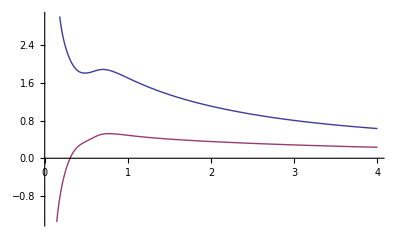

```mathematica
Plot[{Re[σ1[En]],Im[σ1[En]]},{En,.07,4}]
```

σ1 has a zero in its imaginary part at about 0.3 GeV, which appears to create quite a few problems in the parameters that are used in the corrections.

I decided to interpolate a smooth curve to the following two parameters, so that Mathematica wouldn't have to integrate every time they were called. This speeded up things tremendously.

```mathematica
Z=Quiet[Interpolation[Table[{En,U[0,En]/(-I*4*Pi*σ1[En]*β[En])},{En,.31,4.1,.1}]]];(*Unitless*)
γ=Quiet[Interpolation[Table[{En,(Log[U[0,En]]-Log[U[1,En]])},{En,.31,4.1,.1}]]];(*(c/GeV)^2*)
```

Here are a bunch of parameters that Wallace has defined in his paper.

```mathematica
γ1[En_]:=γ[En]*β[En]/(γ[En]+β[En])(*(c/GeV)^2*)
αnL[En_,n_,L_]:=If[n==1,(2*(γ[En]+B)^-1+L*(β[En]+B)^-1)^-1,If[n==2,((γ[En]+B)^-1+(γ1[En]+B)^-1+L*(β[En]+B)^-1)^-1,If[n==3,(2*(γ1[En]+B)^-1+L*(β[En]+B)^-1)^-1]]]
an[En_,n_]:=If[n==1,(γ[En]+B)^-2,If[n==2,-2*σ1[En]*(γ1[En]/γ[En])*(γ[En]+B)^-1*(γ1[En]+B)^-1,If[n==3,σ1[En]^2*(γ1[En]/γ[En])^2*(γ1[En]+B)^-2]]]
bn[En_,n_]:=If[n==1,(γ[En]+B)^-3,If[n==2,-σ1[En]*(γ1[En]/γ[En])*(γ1[En]+B)^-1*(γ[En]+B)^-1*((1-B*γ1[En]/(β[En]*(B+γ1[En])))/(γ[En]+B)+(1-γ1[En]/β[En])/(γ1[En]+B)),If[n==3,σ1[En]^2*(γ1[En]/γ[En])^2*(γ1[En]+B)^-3*(1-B*γ1[En]/(β[En]*(B+γ1[En])))*(1-γ1[En]/β[En])]]]
γ2[En_]:=γ[En]*β[En]/(β[En]+2*γ[En])(*(c/GeV)^2*)
βnL[En_,n_,L_]:=If[n==1,(γ[En]/2+B)^-1+L*(β[En]+B)^-1,If[n==2,(γ2[En]/2+B)^-1+L*(β[En]+B)^-1]]
cn[En_,n_]:=If[n==1,(γ[En]-2*B)*(γ[En]+2*B)^-2,If[n==2,-σ1[En](γ2[En]/γ1[En])*(γ2[En]+2*B)^-1*(1-2*γ2[En]/γ[En]+2*(γ2[En])^2/(γ[En]*(γ2[En]+2*B)))]]
dn[En_,n_]:=If[n==1,γ[En]*(γ[En]+2*B)^-3,If[n==2,
-σ1[En]*(γ[En])^-2*(γ2[En]/(γ2[En]+2*B))^3]]
```

```mathematica
Fcm[q_]:=Exp[-B*q^2/A]
EnL[En_]:=En+m
s[En_]:=m^2+M^2+2*M*EnL[En]
ϵ[En_]:=EnL[En]/(M/Sqrt[s[En]])
P[En_]:=Sqrt[EnL[En]^2-m^2]
k[En_]:=P[En]*(M/Sqrt[s[En]])
s2[En_]:=m^2+m^2+2*m*EnL[En]
ϵ2[En_]:=EnL[En]*(m/Sqrt[s2[En]])
κ[En_]:=P[En]*(m/Sqrt[s2[En]])
ηO[En_]:=(1-ϵ[En]/M)*(m+M)/Sqrt[s[En]]
ηD[En_]:=(1-ϵ[En]/ϵ2[En]+(A-1)*ϵ[En]/M)*(m+M)/Sqrt[s[En]]
```

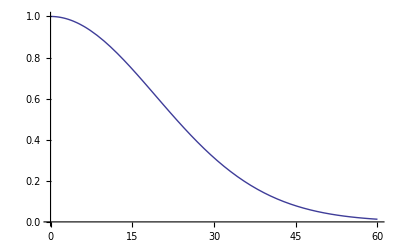

```mathematica
Plot[Fcm[2*k[1.05]*Sin[θ*Pi/360]],{θ,0,60}]
```

```mathematica
B
```

12.0009

```mathematica
F0[En_(*GeV/c^2*),q_]:=-2*I*k[En]*Exp[B*q^2/A]*(B+β[En])*ℏc^2*Sum[Binomial[A,j]/j*(-σ[En]*(1-I*ρ[En])/(8*Pi*(B+β[En])*ℏc^2))^j*Exp[-(B+β[En])*q^2/j],{j,1,A}]
```

```mathematica
σHe4[En_(*MeV*)]:=20*Pi*r^2*(1+2*r^(-2)*gamma[En]^2)*Sum[Binomial[4,j]*(-1)^(j+1)/j*(σ[En]/(2*Pi*r^2*(1+2*r^-2*gamma[En]^2)))^j*Re[(1-I*α[En])^j],{j,1,4}](*This is in mb*)
```

```mathematica
FO1 [En_(*GeV/c^2*),q_(*c/GeV*)]:=A*(A-1)*Fcm[q]*ηO[En]*ℏc^3*(β[En]*σ1[En]*Z[En])^2/(2*(2*Pi*(B+β[En]))^(1/2))*Sum[Binomial[A-2,L]*(-σ1[En]*β[En]/(B+β[En]))^L*Sum[αnL[En,n,L]/ℏc^2*(an[En,n]-4*αnL[En,n,L]*bn[En,n]*(1-αnL[En,n,L]q^2))*Exp[-αnL[En,n,L]*q^2],{n,1,3}],{L,0,A-2}]
```

```mathematica
FD1[En_(*GeV/c^2*),q_(*c/GeV*)]:=A*Fcm[q]*ηD[En]*(β[En]*σ1[En]*Z[En])^2*ℏc/(2*γ[En]*Sqrt[2*Pi*γ[En]])*Sum[Binomial[A-1,L]*(-σ1[En]*β[En]/(B+β[En]))^L*Sum[βnL[En,n,L]/ℏc^4*(cn[En,n]-4*βnL[En,n,L]*dn[En,n]*(1-βnL[En,n,L]*q^2))*Exp[-βnL[En,n,L]*q^2],{n,1,2}],{L,0,A-1}]
```

```mathematica
(4*Pi)/k[1]*Im[F0[1,0]]*10//Timing
```

{0.001,141.079}

```mathematica
σHe4[1]//Timing
```

{0.001,141.079}

```mathematica
(4*Pi)/k[1]*Im[FO1[1,0]]*10//Timing
```

{0.008999,-1.65615}

```mathematica
(4*Pi)/k[1]*Im[FD1[1,0]]*10//Timing
```

{0.004999,9.86259}

InterpolatingFunction::dmval: Input value {-2.2642000513654574`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.10391312646535716`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

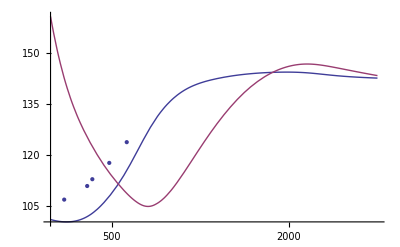

```mathematica
Show[LogLinearPlot[{(4*Pi)/k[En/1000]*Im[F0[En/1000,0]]*10,(4*Pi)/k[En/1000]*Im[F0[En/1000,0]+FO1[En/1000,0]+FD1[En/1000,0]]*10},{En,310,4010}],σHe4LP]
```

This graph below should be a reproduction of Fig 3 from the Wallace. The uncorrected curve is pretty good, but the corrections don't seem to be correct.

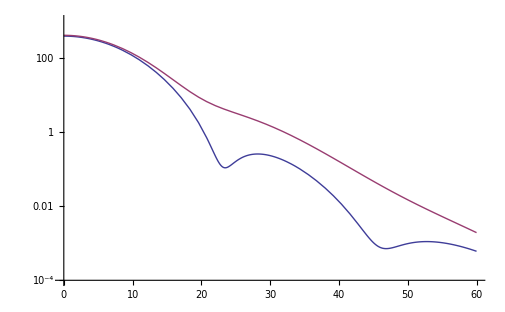

```mathematica
LogPlot[{Abs[F0[1.05,2*k[1.05]*Sin[θ*Pi/360]]]^2*200,Abs[F0[1.05,2*k[1.05]*Sin[θ*Pi/360]]+FO1[1.05,2*k[1.05]*Sin[θ*Pi/360]]+FD1[1.05,2*k[1.05]*Sin[θ*Pi/360]]]^2*200},{θ,0,60},PlotRange->{.0001,1000}]
```

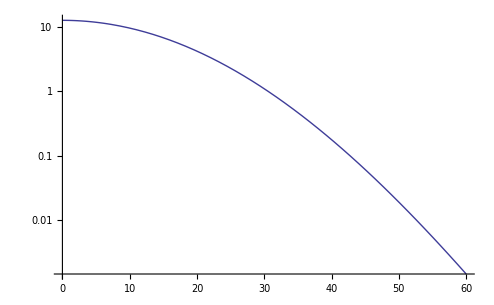

```mathematica
LogPlot[Abs[FD1[1.05,2*k[1.05]*Sin[θ*Pi/360]]]^2*200,{θ,0,60}]
```

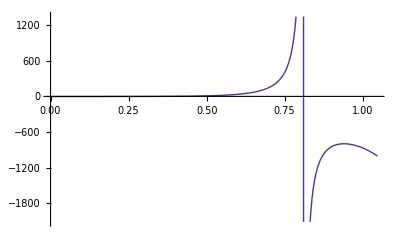

```mathematica
Plot[ηO[1.05]*(1-2*k[1.05]*Sin[t/2]^2*(B+β[1.05]))/(ηD[1.05]*(1-β[1.05]*2*k[1.05]*Sin[t/2]^2)*Exp[-B*2*k[1.05]*Sin[t/2]^2/2]/(A-1)),{t,0,Pi/3}]
```

```mathematica
Abs[F0[1.05,2*k[1.05]*Sin[0/2]]]^2
```

1.93079